```mathematica
Clear["Global`*"]
```

```mathematica
(*Модель Франца-Нодвика*)
```

```mathematica
L=3;(*m*)
NN=300;(*ppm*)
NN=6.62*10^22*NN;(*1/m^3*)
σ=2.5*10^-24;(*m*)
deff=7*10^-6;(*m*)
λ=1064*10^-9;
Aeff=Pi/4*deff^2;(*m^2*)
τ=100*10^-9;(*s*)
h=6.63 10^-34;(*Си*)
c=3*10^8;(*m/s*)
inv=NN*per;(*1/m^3*)
```

```mathematica
Ps=Aeff* h c/λ ;(*коэффициент перевода из плотности потока в мощность*)
Int0r[x_]=HeavisidePi[(x-τ/2)/τ];
i0r=E0/Integrate[Int0r[t],{t,-∞,∞}];
Int0r[x_]:=HeavisidePi[(x-τ/2)/τ]*i0r;
Ir[t_,z_]:=Int0r[t-z/c]/(1-(1-Exp[-σ*inv*z])*Exp[-2*σ*c*Integrate[Int0r[x]/Ps/c,{x,-∞,t-z/c}]]);
Manipulate[Plot[Ir[t,L]/.per->0.01/.E0->10^a,{t,0,2τ},PlotRange->All],{a,-6,-2}]
```

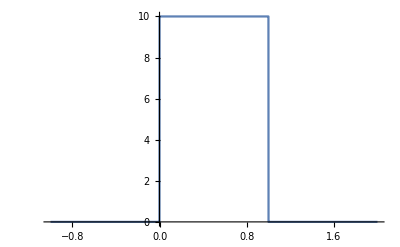

```mathematica
Plot[Int0r[t]/.E0->10^-6,{t,-τ,2τ},PlotRange->All]
```

```mathematica
(*Среднеквадратичная длительность*)
τr1=NIntegrate[t*Ir[t,L]/.per->0.01/.E0->10^-6,{t,L/c,L/c+τ}]/NIntegrate[Ir[t,L]/.per->0.01/.E0->10^-6,{t,L/c,L/c+τ}];
τr2=NIntegrate[t*t*Ir[t,L]/.per->0.01/.E0->10^-6,{t,L/c,L/c+τ}]/NIntegrate[Ir[t,L]/.per->0.01/.E0->10^-6,{t,L/c,L/c+τ}];
τq=Sqrt[τr2-τr1^2]
```

2.89554×10^-8

```mathematica
Int0g[x_]=PDF[NormalDistribution[0,τ/Sqrt[2]],x];
i0g=E0/Integrate[Int0g[t],{t,-∞,∞}];
Int0g[x_]=PDF[NormalDistribution[0,τ/Sqrt[2]],x]*i0g;
Ig[t_,z_]:=Int0g[t-z/c]/(1-(1-Exp[-σ*inv*z])*Exp[-2*σ*c*Integrate[Int0g[x]/Ps/c,{x,-∞,t-z/c}]]);
Manipulate[Plot[Ig[t+L/c,L]/.per->0.01/.E0->10^a,{t,-5τ,5τ},MaxRecursion->2,PlotRange->All],{a,-6,-2}]
```

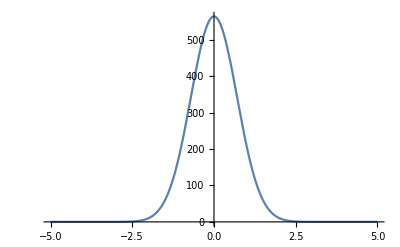

```mathematica
Plot[Int0g[t]/.E0->10^-4,{t,-5τ,5τ},PlotRange->All]
```

```mathematica
τr1=NIntegrate[t*Ig[t,L]/.per->0.01/.E0->10^-6,{t,-10τ,10τ}]/NIntegrate[Ig[t,L]/.per->0.01/.E0->10^-6,{t,-10τ,10τ}];
τr2=NIntegrate[t*t*Ig[t,L]/.per->0.01/.E0->10^-6,{t,-10τ,10τ}]/NIntegrate[Ig[t,L]/.per->0.01/.E0->10^-6,{t,-10τ,10τ}];
τq=Sqrt[τr2-τr1^2]
```

7.22327×10^-8